# Stabilizer Codes in the Quantum Framework

The framework's stabilizer engine holds a state: an n-qubit state stored as the Pauli operators that fix it, pushed through Clifford gates in the Heisenberg picture. This layer holds a code: a subspace fixed by a commuting group of Pauli checks, chosen so that the errors we care about push a state out of that subspace in a way we can detect and undo.

The difference matters. A stabilizer state is fixed by n independent checks and is a single point. A stabilizer code is fixed by m<n of them, so it is a subspace of dimension 2^(n-m), and the k==n-m qubits' worth of room inside it is where the protected information lives. Everything below follows from that one shift.

What this note covers, in order: the code object and how it is stored; the Pauli layer beneath it; the structural quantities (logical operators, distance); syndromes and decoding; encoding circuits; building codes out of other codes; noise; and the figure of merit the whole subject is about — whether a logical qubit survives. Then the same question asked honestly: the circuit that measures the checks, the faults inside it, detectors, and a memory experiment run over several rounds — ending with the whole thing written out in Stim's syntax and checked against it.

One thing here is not available anywhere else, and it is worth naming up front. Because the noise rate may be left symbolic, the logical error rate comes back as an exact polynomial rather than a sampled estimate. A fast simulator answers "about 0.0022 at p = 0.01"; this answers "10 p^2-200 p^3/9+160 p^4/9-128 p^5/27, for every p". That is what exactness and symbolic generality buy, and it is the one move a Monte Carlo simulator structurally cannot make. It holds all the way up: even with every gate, reset and readout of the syndrome-extraction circuit failing, the answer is still a closed-form polynomial, and the last sections use that to say two things about fault tolerance that are awkward to state any other way.

## Definition

The code layer is a development package under OngoingProjects/QEC/, not yet part of the paclet, so this page loads both the framework and the layer itself. Symbols introduced in this section stay bound for the whole note.

Two notes on why this cell exists at all, since documentation pages normally have no setup code. A reference page gets an ExampleInitialization cell from its template, and the converter fills it from the frontmatter Context:; the tech-note template has no such cell, so the converter has nothing to fill and a reader opening the notebook cold would find no context loaded. And the code layer is not in any paclet yet, so no context declaration could load it. Both lines go away when the layer moves into the paclet.

Load the framework and locate the code layer. The cell reports whether it worked, because a setup cell that fails quietly leaves every later cell showing an unevaluated symbol — which looks like a broken package rather than a path that did not resolve:

```mathematica
Needs["Wolfram`QuantumFramework`"];

qecCore = SelectFirst[
    {
        (* beside this notebook: docs/Tutorials/ up two levels *)
        Quiet @ Check[FileNameJoin[{ParentDirectory[NotebookDirectory[], 2], "QECCore", "QECCore.wl"}], $Failed],
        (* from a repo checkout of the framework, when that is the one loaded *)
        FileNameJoin[{ParentDirectory[DirectoryName[FindFile["Wolfram`QuantumFramework`"], 2]],
            "OngoingProjects", "QEC", "QECCore", "QECCore.wl"}],
        (* from the working directory *)
        FileNameJoin[{Directory[], "QECCore", "QECCore.wl"}]
    },
    StringQ[#] && FileExistsQ[#] &,
    $Failed
];

If[ qecCore === $Failed,
    Failure["QECCoreNotFound", <|"MessageTemplate" ->
        "Could not locate QECCore/QECCore.wl. Get it by hand, then run the rest of the page."|>],
    Get[qecCore];
    MemberQ[$ContextPath, "Wolfram`QuantumFramework`QEC`"]
]
```

True

A True there means the layer is loaded and its symbols are on the context path, so every cell below runs. A Failure means only that the file was not where this page guessed: Get the QECCore/QECCore.wl beside it by hand and continue from the next cell.

## The code object

A code is built from its stabilizer generators, given as Pauli strings. The constructor checks what a code needs: equal length, pairwise commuting, independent.

The five-qubit code, from its four checks:

```mathematica
QECCode[{"XZZXI", "IXZZX", "XIXZZ", "ZXIXZ"}]
```

QECCode[<|CheckMatrix -> {{1, 0, 0, 1, 0, 0, 1, 1, 0, 0}, {0, 1, 0, 0, 1, 0, 0, 1, 1, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 1, 1}, {0, 1, 0, 1, 0, 1, 0, 0, 0, 1}}, Phases -> {0, 0, 0, 0}, Qubits -> 5|>]

The textbook codes are available by name:

```mathematica
QECCode["SteaneCode"]["Generators"]
```

{IIIXXXX,XIXIXIX,IXXIIXX,IIIZZZZ,ZIZIZIZ,IZZIIZZ}

Its parameters are the [[n,k,d]] of the literature — physical qubits, logical qubits, distance:

```mathematica
QECCode["SteaneCode"]["Parameters"]
```

{7,1,3}

A code is stored the way the engine stores a tableau, and for the same reason: not as Pauli strings but as a check matrix of binary symplectic rows plus a separate list of phases. Strings are an input and output convention, never the thing computations run on.

The check matrix of the Steane code, X half on the left, Z half on the right:

```mathematica
ArrayPlot[QECCode["SteaneCode"]["CheckMatrix"], Mesh -> All, ImageSize -> 260]
```

-Graphics-

The block structure is visible: three generators with support only in the X half, three only in the Z half. That is what makes it a CSS code, and it is a property the object will confirm directly.

```mathematica
QECCode["SteaneCode"]["CSSQ"]
```

True

## Codes and states

It is worth being precise about where this layer sits, because the engine already represents stabilizer states and the two objects are easy to confuse.

A PauliStabilizerpaclet:Wolfram/QuantumFramework/ref/PauliStabilizerWolfram/QuantumFramework Package Symbol holds n independent commuting generators on n qubits. That pins a single state — there is exactly one joint +1 eigenvector — and the engine's job is to push it through Clifford gates and measure it. A QECCode holds m<n generators. That does not pin a state; it pins a 2^(n-m)-dimensional subspace, and the questions worth asking about it are different: which operators act on the space without leaving it, how far apart its members are, what circuit prepares one.

The two meet constantly, and deliberately in one direction: the code hands work to the engine rather than reimplementing it. Completing a code's generators to a full set of n pins one fiducial codeword, and that codeword is an engine object:

```mathematica
Head[QECCode["SteaneCode"]["PauliStabilizer"]]
```

PauliStabilizer

That is how an encoding circuit is validated, how the physical correction cycle runs, and how syndromes are cross-checked: the answer computed here symplectically is compared against the answer the engine measures on an actual state. The two agree because they share a row format, not because they were written to agree.

The division of labour also runs the other way. Anything genuinely about a state at scale — long Clifford circuits, measurement, entanglement entropy — belongs in the engine, where it has a compiled bulk path; the encoder here delegates its gate application to exactly that path rather than folding gates one at a time.

## Paulis and phases

Underneath the code object, a Pauli is a row of bits: x_1…x_n, then z_1…z_n, then a phase. It is the same layout the stabilizer engine uses internally, so the two halves of the framework speak one format.

A Pauli is one object, QECPauli. It is built from a string or a row, prints as its string, and holds the row:

```mathematica
QECPauli["XZZXI"]
```

QECPauli[XZZXI]

Its properties are the forms and facts a Pauli has — "String", "Vector", "Weight", "Phase", "Support", "Matrix", "QuantumOperator" — and the two relations, "CommuteQ" and "Product" (also written **). The row, for one:

```mathematica
QECPauli["XZZXI"]["Vector"]
```

{1,0,0,1,0,0,1,1,0,0,0}

One deliberate difference from the engine: the phase lives in Z_4, meaning an overall factor i^e, where the engine's tableau carries a single sign bit. The reason is that the Pauli group is not closed under multiplication with a sign alone.

The product of X and Z is not Y:

```mathematica
(QECPauli["X"] ** QECPauli["Z"])["String"]
```

-iY

A sign bit cannot express that factor, so a package that tracks signs only must either drop the phase or refuse to multiply. Carrying Z_4 costs one integer per Pauli and makes the algebra closed:

```mathematica
(QECPauli["XIX"] ** QECPauli["IZZ"])["String"]
```

-iXZY

Hermitian Paulis — every stabilizer generator, every error — have even phase, and half of it is exactly the engine's sign bit, so nothing is lost in translation.

Commutation is the symplectic product of two rows, which is what makes it cheap:

```mathematica
Outer[QECPauli[#1]["CommuteQ", #2] &, {"XZZXI", "IXZZX", "XIXZZ", "ZXIXZ"}, {"XZZXI", "IXZZX", "XIXZZ", "ZXIXZ"}]
```

{{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True}}

## Logical operators and distance

The logical information lives in the Paulis that commute with every check but are not themselves in the check group — the normalizer modulo the stabilizer, N(S)\S. Finding a canonical pair is done on the standard form of the check matrix, following the closed formulas of Gottesman's thesis, section 4.1.

The logical X of the five-qubit code, which is the operator that thesis reports:

```mathematica
QECCode["5QubitCode"]["LogicalX"]
```

{ZIIZX}

And its logical Z:

```mathematica
QECCode["5QubitCode"]["LogicalZ"]
```

{ZZZZZ}

The distance is the minimum weight of a logical operator, and it is the number that says how many errors the code can correct: ⌊(d-1)/2⌋ of them.

```mathematica
QECCode["SteaneCode"]["Distance"]
```

3

Computing it exactly is NP-hard in general, so the search is a search. Two things keep it honest on the codes that fit. The logical operators from the standard form are themselves in N(S)\S, so their minimum weight is an upper bound and the scan never runs past it; and the syndromes of a whole weight class are computed as one matrix product rather than one call per candidate. The witness that realises the distance is available, so the answer can be checked rather than trusted:

```mathematica
QECCode["5QubitCode"]["MinimumWeightLogical"]
```

ZIIZX

On this code the witness is the logical X itself, which is a coincidence of the five-qubit code being as tight as it is: there is no lighter operator anywhere in N(S)\S than the canonical pair the standard form produces.

That witness is a logical operator, and its weight is the distance:

```mathematica
{QECPauli[QECCode["5QubitCode"]["MinimumWeightLogical"]]["Weight"],
 QECCode["5QubitCode"]["LogicalPauliQ", QECCode["5QubitCode"]["MinimumWeightLogical"]]}
```

{3,True}

## Syndromes and decoding

An error either commutes or anticommutes with each check. The pattern of anticommutations is the syndrome, and it is the only thing a measurement is allowed to reveal.

That last clause is the whole trick, and it is worth spelling out. Measuring a check operator on a codeword is a projective measurement, and on a state already in the code space it returns +1 with certainty and disturbs nothing. On a state that an error has pushed out, it returns -1 — but the outcome depends only on whether the error anticommutes with that check, and every logical operator commutes with every check by construction. So the measurement cannot distinguish (|0)_L⟩ from (|1)_L⟩, or any superposition of them, no matter how many checks are measured. The syndrome carries information about the error and none about the logical state. Reading it is free.

What the syndrome does not do is identify the error. Two errors differing by a stabilizer produce the same syndrome and need the same correction — they are genuinely the same problem, and a code where many errors share a coset is called degenerate. Two errors differing by a logical operator also produce the same syndrome and need different corrections, and no measurement can tell them apart. That ambiguity is the entire difficulty of decoding, and the distance is the measure of how much room the code leaves before it bites.

The syndrome of a single X error on the Steane code:

```mathematica
QECCode["SteaneCode"]["Syndrome", "XIIIIII"]
```

{0,0,0,0,1,0}

A sign on the error cannot change which checks it anticommutes with, so the syndrome ignores it:

```mathematica
QECCode["SteaneCode"]["Syndrome", "-XIIIIII"] === QECCode["SteaneCode"]["Syndrome", "XIIIIII"]
```

True

Decoding is the inverse problem: given the syndrome, infer the error. The simplest honest answer is a table from syndrome to a minimum-weight error producing it, built out to the weight the code actually guarantees:

```mathematica
(QECPauli[#]["String"] &) /@ QECCode["BitFlipCode"]["Decoder"]
```

<|{0,0}→III,{1,0}→XII,{1,1}→IXI,{0,1}→IIX|>

Running the full cycle — syndrome, inference, correction — reports what happened rather than a bare success flag:

```mathematica
Dataset[QECCode["SteaneCode"]["CorrectionCycle", "YIIIIII"]]
```

The distinction the report draws matters. A residual that lands in the stabilizer group is a correction that worked; one that lands in N(S)\S is a silent logical error, the failure mode the whole subject exists to bound; and a syndrome the table cannot decode is a third thing again. On the bit-flip code, a Z error is invisible to every check:

```mathematica
QECCode["BitFlipCode"]["CorrectionCycle", "ZII"]["Outcome"]
```

LogicalError

## Encoding circuits

A code is not useful until something prepares a codeword. The encoder follows Procedure 6.6 of Gottesman's 2026 book, with the gate-to-row-operation dictionary of its Table 6.1.

The construction is worth understanding, because it is the one place where a linear-algebra fact turns directly into a circuit. Write the m generators as the columns of a 2n×m binary matrix, the X parts stacked above the Z parts. Left-multiplying by a Clifford gate is then a row operation on that matrix, and the dictionary is small and fixed: a Hadamard on qubit q swaps the q-th X row with the q-th Z row; a phase gate adds the X row into the Z row; a CNOT adds one X row to another and one Z row back the other way; a controlled-Z crosses X into Z between two qubits. Relabelling which product of generators counts as a generator is a column operation, and costs no gate at all.

So the problem becomes Gaussian elimination with two kinds of move, and the target is the matrix of the trivial code — every generator a single Z. Reduce to it, record the gates used, and the encoder is that sequence run backwards, since every gate in the dictionary is its own inverse except the phase gate, whose inverse is three of itself.

One step remains after inverting. Reducing and re-inflating gets the group right but not necessarily the signs: the prepared state is stabilized by each generator up to a minus. A Pauli correction fixes it, and finding it is again linear algebra — solve over GF(2) for the Pauli whose symplectic products with the generators match the pattern of wrong signs, then apply it.

The book's own recipe for that fixup is to prepend an X on each qubit whose generator came out negative; the package instead solves the general system, which handles the completed generator set in one step. Both are correct and produce circuits of the same length, on every code tested.

The encoding circuit of the five-qubit code:

```mathematica
QECCode["5QubitCode"]["EncodingCircuit"]
```

QuantumCircuitOperator[…]

The reduction can only ever emit the five gates of that dictionary, so the circuit's vocabulary is fixed in advance — here, four of them:

```mathematica
DeleteDuplicates[First /@ QECCode["SteaneCode"]["EncodingGates"]]
```

{H,CZ,SWAP,CNOT}

The sign fixup is the one thing that can add to that vocabulary, and on codes that need it a Pauli appears alongside the Cliffords:

```mathematica
DeleteDuplicates[First /@ QECCode["5QubitCode"]["EncodingGates"]]
```

{H,CZ,CNOT,X}

Reducing and inverting prepares a state stabilized by each generator up to sign; a Pauli fixup solved over GF(2) corrects the signs that came out wrong. Whether the result is really a codeword is checked against the engine, by measuring every check on the prepared state:

```mathematica
AllTrue[{"BitFlipCode", "PhaseFlipCode", "ShorCode", "5QubitCode", "SteaneCode"},
    QECCode[#]["EncodingCircuitValidQ"] &]
```

True

## Building codes from other codes

Three constructions of Gottesman's thesis, section 3.5, plus the CSS construction of chapter 5 of the book, all return the same code object, so everything above works on the result unchanged.

A CSS code is built from classical parity-check matrices: rows of one become X-type checks, rows of the other Z-type, and they commute exactly when the matrices are orthogonal over GF(2). Fed the classical Hamming matrix, the construction reproduces the Steane code:

```mathematica
QECCode["CSS", {{0, 0, 0, 1, 1, 1, 1}, {0, 1, 1, 0, 0, 1, 1}, {1, 0, 1, 0, 1, 0, 1}}]["Parameters"]
```

{7,1,3}

"Reproduces" deserves care: the generators come out in a different order, so the claim is about the stabilizer group, checked in both directions and with signs:

```mathematica
Module[{css = QECCode["CSS", {{0, 0, 0, 1, 1, 1, 1}, {0, 1, 1, 0, 0, 1, 1}, {1, 0, 1, 0, 1, 0, 1}}], steane = QECCode["SteaneCode"]},
    AllTrue[steane["GeneratorVectors"], css["StabilizerMemberQ", #] &] &&
    AllTrue[css["GeneratorVectors"], steane["StabilizerMemberQ", #] &]
]
```

True

Concatenation re-encodes each qubit of an outer code with an inner one. The phase-flip code inside the bit-flip code is the Shor code, which is how Shor found it:

```mathematica
QECConcatenate[QECCode["PhaseFlipCode"], QECCode["BitFlipCode"]]["Parameters"]
```

{9,1,3}

Distances multiply only as a lower bound, not an equality. The bit-flip code has quantum distance 1, yet concatenating it under the five-qubit code buys distance 5, not 3, because it still corrects bit flips at weight 3:

```mathematica
QECConcatenate[QECCode["5QubitCode"], QECCode["BitFlipCode"]]["Parameters"]
```

{15,1,5}

Qubit removal is surgery: recombine the generators so that exactly one ends in X and one in Z at the removed qubit, drop those two — they become the new logical pair — and truncate the rest. On the five-qubit code it produces the [[4,2,2]] code, with the generators Gottesman reports:

```mathematica
QECRemoveQubit[QECCode["5QubitCode"]]["Generators"]
```

{XZZX,YXXY}

## Noise

None of the above says anything about whether a code works, because a code only means something relative to a noise model. The simplest honest one is code-capacity noise: each qubit independently suffers X, Y or Z with fixed probabilities, between rounds, with perfect check measurements. That last assumption is a real one, and the sections after the next give it up.

Depolarizing noise, with the rate left symbolic:

```mathematica
QECNoiseModel["Depolarizing", p]["Probabilities"]
```

{1-p,p/3,p/3,p/3}

Because the errors are independent and identically distributed, the probability of a specific error depends only on how many X, Y and Z it carries — never on where they sit. That collapses a sum over 4^n errors into a sum over the far smaller set of weight profiles, and it is what makes everything in the next section exact rather than sampled:

```mathematica
QECNoiseModel["Depolarizing", p]["ErrorProbability", "XIIIIII"]
```

1/3 (1-p)^6 p

The model is not a private random-number generator: it maps onto the engine's own channels, so the probabilities can be checked against what the engine actually does to a stabilizer state. Note that the conventions differ — the engine's depolarizing parameter gives each Pauli a quarter of it, this model spreads its rate over three — so the constructor converts, and this is the test that the conversion is right:

```mathematica
Module[{noise = QECNoiseModel["Depolarizing", p]},
    Simplify[Sort[noise["QuantumChannel", {1}][PauliStabilizer[1]][[All, 1]]] == Sort[noise["Probabilities"]]]
]
```

True

For codes too large to enumerate, the model samples. A bit-flip channel can only produce X errors, and does:

```mathematica
BlockRandom[SeedRandom[7]; QECNoiseModel["BitFlip", 1/3]["RandomErrors", 6, 5]]
```

{XXIIXX,XXIIXX,IIIIXI,IIXXXI,XXIXXI}

## The logical error rate

This is the question the subject is about. Prepare a codeword, hit it with an error drawn from the noise, measure the checks, decode, correct, and ask whether the logical qubit got flipped.

One observation makes it exact. Label every Pauli error by two things: which checks it anticommutes with (its syndrome) and which logical operators it anticommutes with (its class). Both are the same question, so both are one matrix product over GF(2). Two errors sharing a label differ by a stabilizer, so the label's fibre is the coset; decoding is guessing the class half from the syndrome half; and a correction succeeds exactly when the guess was right. No residual algebra per trial — the label already decides it.

The exact logical error rate of the five-qubit code under depolarizing noise:

```mathematica
Expand[QECLogicalErrorRate[QECCode["5QubitCode"], QECNoiseModel["Depolarizing", p]]]
```

10 p^2-(200 p^3)/9+(160 p^4)/9-(128 p^5)/27

The leading term is not a fit. The five-qubit code is perfect, so every weight-one error is corrected and every weight-two error fails; there are 9Binomial[5, 2]==90 of the latter, each of probability (p/3)^2(1-p)^3, giving exactly 10 p^2. The polynomial is checkable by hand.

The Steane code, which is not perfect, so some weight-two errors survive:

```mathematica
Normal[Series[QECLogicalErrorRate[QECCode["SteaneCode"], QECNoiseModel["Depolarizing", p]], {p, 0, 3}]]
```

(49 p^2)/3-56 p^3

The strongest check available on any of this is a closed form that owes the package nothing. The repetition code under bit-flip noise fails exactly when a majority of its qubits flips, which is a binomial tail:

```mathematica
Simplify[
    QECLogicalErrorRate[QECCode["Repetition", 5], QECNoiseModel["BitFlip", p]] ==
        Sum[Binomial[5, j] p^j (1 - p)^(5 - j), {j, 3, 5}]
]
```

True

With an exact rate per code, the threshold — the rate below which adding qubits helps and above which it hurts — stops being a fit to sampled curves and becomes a crossing of polynomials. For repetition codes under bit flips it sits at exactly one half:

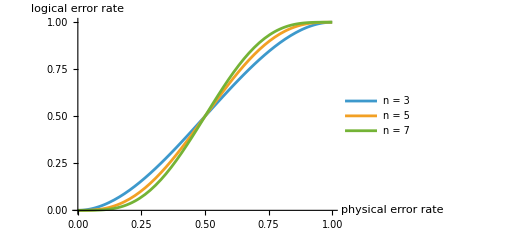

```mathematica
Plot[
    Evaluate[Table[QECLogicalErrorRate[QECCode["Repetition", n], QECNoiseModel["BitFlip", p]], {n, {3, 5, 7}}]],
    {p, 0, 1},
    PlotLegends -> {"n = 3", "n = 5", "n = 7"},
    AxesLabel -> {"physical error rate", "logical error rate"},
    ImageSize -> 380
]
```

Below one half the longer code is better and the gap widens with n; above it the order reverses. That crossing is the whole argument for error correction, and here it is an exact statement about three polynomials rather than a claim about three sampled curves.

For codes past the enumeration limit the same quantity is estimated by drawing errors, and the two routes are independent implementations that check each other:

```mathematica
BlockRandom[SeedRandom[3];
    {N[QECLogicalErrorRate[QECCode["SteaneCode"], QECNoiseModel["Depolarizing", 1/20]]],
     QECLogicalErrorRate[QECCode["SteaneCode"], QECNoiseModel["Depolarizing", 1/20], 100000]}
]
```

{0.034361,0.03409}

The decoder is maximum likelihood: for each syndrome it picks the coset carrying the most probability, not the lightest representative. The "Decoder" option chooses, and the difference is not academic. Against the lookup table — the decoder anyone can afford on a large code — coset weighing wins in two separate ways. On the degenerate nine-qubit Shor code, under ordinary symmetric noise, because many light errors share a coset and the table sees only one of them: 13 p^2 against 31 p^2. And on the Steane code under biased noise, as real hardware is, with Z ten times likelier than X: 651 p^2/25 against 756 p^2/25. On a perfect code like the five-qubit one there is nothing to gain and the two agree exactly.

The biased case:

```mathematica
Coefficient[
    Normal[Series[
        QECLogicalErrorRate[QECCode["SteaneCode"], QECNoiseModel[<|"X" -> p/10, "Y" -> p/10, "Z" -> p|>]],
        {p, 0, 2}]],
    p, 2]
```

651/25

## The code as quantum operations

Everything so far has been symplectic: rows, syndromes, cosets. The same code is also a set of ordinary quantum objects — an encoding isometry, a code-space projector, a syndrome measurement, recovery channels, and one effective channel on the logical qubit — and those are what the rest of the framework composes with. The code gives them directly.

The encoder is the isometry V from the logical qubit into the physical ones:

```mathematica
QECCode["BitFlipCode"]["Encoder"]
```

QuantumOperator[…]

Its columns are the codewords, and they are stated in the code's own logical basis: (|0)_L⟩ is the +1 eigenstate of the Z̄ that code["LogicalZ"] reports, (|1)_L⟩ the -1 one. That is not automatic. The encoding circuit of the five-qubit code sends |00000⟩ to the -1 eigenstate of that Z̄ — still a valid encoder, but with its own labels — so the codewords are moved into the code's basis before they are handed out:

```mathematica
With[{five = QECCode["5QubitCode"]},
    With[{z = Normal[QECPauli[First[five["LogicalZ"]]]["Matrix"]]},
        Simplify[Conjugate[#] . z . #] & /@ (Normal[#["StateVector"]] & /@ five["Codewords"])
    ]
]
```

{1,-1}

The syndrome measurement is a QuantumMeasurementOperator with one projector ∏_i (1+(-1)^s_i g_i)/2 per syndrome, outcome i being the syndrome IntegerDigits[i - 1, 2, m]. An X on the middle qubit of the bit-flip code trips both checks, syndrome {1,1}, the fourth outcome, with certainty — and the recovery for that syndrome puts the codeword back:

```mathematica
Module[{bf = QECCode["BitFlipCode"], zero, hit},
    zero = First[bf["Codewords"]];
    hit = QuantumOperator["IXI"][zero];
    <|"syndrome" -> bf["Syndrome", "IXI"],
      "outcome probabilities" -> Values[Normal[bf["SyndromeMeasurement"][hit]["Probabilities"]]],
      "recovered" -> Chop[Normal[bf["Recovery", {1, 1}][QuantumState[hit["DensityMatrix"]]]["DensityMatrix"]] -
          Normal[zero["DensityMatrix"]]] == ConstantArray[0, {8, 8}]|>
]
```

<|syndrome→{1,1},outcome probabilities→{0,0,0,1},recovered→True|>

These four are dense — 2^n-sized — and stop at $QECDenseQubitLimit (10 qubits by default) with a message naming the cheap route. The next one is not dense, and it is the one that matters.

Encode, apply the noise, measure the syndrome, recover, decode: the whole cycle is one channel on the logical qubit. Taken literally that composition runs through a 4^n-dimensional superoperator. But for Pauli noise on a stabilizer code the cycle's net effect is always a logical Pauli — the error times the correction lies in the normalizer — so the logical channel is a Pauli channel with 4^k weights, and those weights are exactly the coset probabilities the maximum-likelihood decoder already computes. So it comes out exact and symbolic:

```mathematica
QECCode["BitFlipCode"]["LogicalPauliProbabilities", QECNoiseModel["BitFlip", p]]
```

<|I→(-1+p)^2 (1+2 p),X→(3-2 p) p^2,Y→0,Z→0|>

and the logical error rate is nothing but one minus its identity weight — on the Steane code, to the last coefficient:

```mathematica
With[{steane = QECCode["SteaneCode"], noise = QECNoiseModel["Depolarizing", p]},
    Simplify[1 - steane["LogicalPauliProbabilities", noise]["I"] - QECLogicalErrorRate[steane, noise]]
]
```

0

code["LogicalChannel", noise] is the same thing as a QuantumChannel on the logical qubits, ready to compose with anything else in the framework. It is a code-capacity object: at circuit level the checks themselves are noisy, the cycle is not one channel, and the rate comes from the detector model instead.

Noise can be given in the framework's own terms, too. A one-qubit QuantumChannel that is a Pauli channel reads back as a noise model — its Kraus operators reduced to Pauli weights, then checked against the channel's superoperator — and is accepted wherever a noise model is:

```mathematica
{QECNoiseModel[QuantumChannel["Depolarizing"[q]]]["Probabilities"],
 Expand[QECLogicalErrorRate[QECCode["Repetition", 3], QuantumChannel["BitFlip"[p]]]]}
```

{{1-(3 q)/4,q/4,q/4,q/4},3 p^2-2 p^3}

A channel that is not Pauli — amplitude damping is the usual one — is refused with its reason rather than twirled silently: its effect on a stabilizer code is not a distribution over Paulis, and choosing to approximate it by one is a modelling decision.

The question under all of this — does the code correct this set of errors? — is the Knill–Laflamme condition, ⟨W_i|E_a^†E_b|W_j⟩==h_ab δ_ij. For Pauli errors it is decided by where E_a^†E_b sits: anticommuting with a check gives 0, in the stabilizer gives its phase, a nontrivial logical breaks the condition. So it is computed on rows, at any size, and the dense definition is only its test:

```mathematica
With[{bf = QECCode["BitFlipCode"]},
    {bf["KnillLaflammeMatrix", {"III", "XII", "IXI", "IIX"}],
     bf["KnillLaflammeMatrix", {"XII", "IXX"}]}
]
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},Missing[NotCorrectable,<|Errors→{XII,IXX},Product→XXX|>]}

The failure names the pair and the logical operator their product is. Asked of every error up to a weight, it reads the distance off:

```mathematica
Table[QECCode["SteaneCode"]["CorrectableQ", "Weight"[t]], {t, 0, 2}]
```

{True,True,False}

These are the spellings the bosonic branch of the project uses for the same questions — "Codewords", "KnillLaflammeMatrix", "CorrectableQ" — so a qubit code and an oscillator code answer them alike.

## Decoders as objects

The decoders behind the rate can be held. QECDecoder[code] is the minimum-weight table, QECDecoder[code, noise] maximum likelihood (or, at circuit level, the detector model's decoder), QECDecoder[dem] the detector model's lightest-fault rule:

```mathematica
With[{d = QECDecoder[QECCode["SteaneCode"]]}, {d["Method"], d["Decode", {0, 0, 0, 1, 1, 1}]}]
```

{MinimumWeight,IIIIIIX}

The fourth constructor is the seam for everything else. QECDecoder[code, f] wraps any function from a syndrome to a correction — PyMatching through ExternalEvaluate, a neural decoder, a lookup — and the rate scores it with the same machinery as the built-ins, through "Decoder" -> dec. The decoder that never corrects anything, on the bit-flip code, fails whenever anything happened:

```mathematica
Simplify[QECLogicalErrorRate[QECCode["BitFlipCode"], QECNoiseModel["BitFlip", p],
    "Decoder" -> QECDecoder[QECCode["BitFlipCode"], If[# === {0, 0}, "III", Missing[]] &]]]
```

p (3-3 p+p^2)

QECLogicalErrorRate returns the rate and only the rate. The full report — the rate, the probability of acceptance, and the joint failure probability — is one argument away, with the same keys whether or not anything was post-selected:

```mathematica
QECLogicalErrorRate[QECCode["SteaneCode"], QECNoiseModel["Depolarizing", 1/10], All]
```

<|Rate→13147289/113906250,Acceptance→1,Failure→13147289/113906250|>

The detector model answers the same questions as dem["LogicalErrorRate"], dem["Acceptance"] and dem["Failure"]; they differ from the plain rate only when a gadget rejects shots, which is where the next sections go.

## Noisy syndrome extraction

Everything so far has assumed the checks are read out perfectly. That assumption is the one a hardware person will not grant, and giving it up is what the rest of this note is about.

There are three levels, and they are the same object with different keys set. At code capacity the data is hit between rounds and the checks are exact — that is everything above. At the phenomenological level the checks additionally lie with some probability, which is the first point at which repeating the measurement means anything. At circuit level there are no "checks" at all: the extraction is written out as a subcircuit and every gate, reset and readout in it can fail; faults attach to circuit locations with one rate per location type, which is a Pauli specialisation of the basic model of Gottesman's §10.1.1.

Each level drops an assumption the one before it made, but they are not three estimates of one number, and the middle one has a name in the literature that is worth carrying: Gottesman's §10.4 introduces the phenomenological model as the standard example of an optimistic assumption, not of a more realistic one.

The level is derived from what you set, not declared:

```mathematica
{QECNoiseModel["Depolarizing", p]["Level"],
 QECNoiseModel["Depolarizing", p, "MeasurementError" -> q]["Level"],
 QECNoiseModel["Circuit", p]["Level"]}
```

{CodeCapacity,Phenomenological,Circuit}

A circuit-level model puts a rate on each kind of location. One number spreads over all of them; an Association sets them separately, and a missing key is zero, which is a clean way to ask what one kind of failure does on its own:

```mathematica
QECNoiseModel["Circuit", <|"TwoQubit" -> p, "Measurement" -> q|>]["Rates"]
```

<|OneQubit→0,TwoQubit→p,Measurement→q,Reset→0,Idle→0|>

Idling is modelled but stays at zero by default, and the next section says why that default is optimistic rather than neutral.

## The extraction circuit

To measure a Pauli generator with an ancilla: rotate each data qubit in the generator's support so that its letter there becomes Z, CNOT those data qubits into the ancilla, rotate back, and measure the ancilla. The ancilla ends up holding the parity of the rotated qubits, which is the generator's eigenvalue.

This is the circuit of Gottesman's §12.1.1, figure 12.1a, and that section's title is worth quoting: Non-Fault-Tolerant Measurement of Paulis. The book's version puts the ancilla in |+⟩ and applies controlled-P from ancilla to data; conjugating each data qubit by the rotation that sends its letter to Z turns that into a controlled-Z ladder, and since H·CZ·H==CNOT the ancilla's Hadamards are absorbed into the ladder. Gate for gate it is the same circuit with the basis change written out rather than folded into "controlled-P".

The rotation is H for an X, the engine's "V" — the square root of X, which sends Y to Z — for a Y, and nothing at all for a Z. A single generator carrying all three letters shows every case at once:

```mathematica
QECCode[{"XYZ"}]["SyndromeCircuit"]["Instructions"]
```

{{R,4},{H,1},{V,2},{CNOT,1,4},{CNOT,2,4},{CNOT,3,4},{H,1},{Vdg,2},{M,4}}

The bit-flip code's generators are pure Z, so its circuit is nothing but CNOTs and measurements — one ancilla per generator, reset before use:

```mathematica
QECCode["BitFlipCode"]["SyndromeCircuit"]["Instructions"]
```

{{R,4},{CNOT,1,4},{CNOT,2,4},{M,4},{R,5},{CNOT,2,5},{CNOT,3,5},{M,5}}

The ancillas are reset and reused between rounds, so a long experiment does not need more of them. Five rounds of the Steane code run on the same thirteen qubits as one:

```mathematica
{QECCode["SteaneCode"]["SyndromeCircuit", 1]["Qubits"],
 QECCode["SteaneCode"]["SyndromeCircuit", 5]["Qubits"]}
```

{13,13}

What the whole thing costs, which is also the number of places a fault can happen:

```mathematica
QECCode["SteaneCode"]["SyndromeCircuit", 3]["GateCounts"]
```

<|R→18,H→72,CNOT→72,M→18|>

Two limits are worth stating, and the first is not a rough edge. The ancillas are bare rather than cat-state-verified, and that is the difference between fault tolerant and not, not a detail alongside gate scheduling: §12.1.1 says of this exact circuit that "a single faulty gate can cause multiple data errors, even if the fault doesn't directly affect the data block". The fix is a verified ancilla feeding Shor (§12.2), Steane (§12.3) or Knill (§12.4) error correction. Using the bare version anyway is a sourced choice rather than a shortcut — §12.5.1: "Frequently people using surface codes don't even bother with Shor EC, instead using the non-FT measurement technique of section 12.1.1 instead" — but that concession belongs to the surface-code setting and is not a general licence.

The second: generators are extracted one after another rather than interleaved into parallel layers, so the circuit is deeper than a real one, and the "Idle" rate is zero. Do not read that as idling being undefined here. §15.5.2 resolves an ill-defined time step by defining one, the longest gate, and charging the padding as storage error; and §15.5.1 shows that less parallelism means more waiting, multiplying the storage rate, with the flat statement that "to have a threshold, it is essential to do parallel gates, at least when the storage error rate p_S is non-zero". Zero idle noise is an optimistic simplification, and it is optimistic in exactly the direction this circuit is already weakest.

Nothing in this circuit is taken on trust. Pushing a Pauli through the emitted instructions and reading the ancilla measurements has to reproduce code["Syndrome", …], which is a matrix product that knows nothing about circuits; the same circuit is also run as an actual stabilizer state on the engine and its checks read by expectation. Both agree, for every weight-one and weight-two error on all five named codes.

## Detectors

Once a check can lie, a syndrome bit on its own is worthless: it can be wrong because the data was hit or because the readout misreported, and one round cannot tell those apart. Repeating the extraction is the old fix (§12.2.2). Decoding the differences rather than the syndromes is a newer one, from the topological-code literature — Dennis, Kitaev, Landahl and Preskill, Topological quantum memory (arXiv:quant-ph/0110143), where repeated noisy measurement turns the history into a lattice in one more dimension:

D_1==S_1,    D_r==S_r⊕S_(r-1),    D_(R+1)==S_final⊕S_R

A detector is a parity that is deterministically zero when nothing goes wrong, so a fired detector is unambiguous evidence of a fault. The last one closes the experiment against a noiseless final readout, where S_final is the syndrome of whatever Pauli is left on the data.

Two things follow from "deterministically zero" that are easy to skip past. It assumes the data enters inside the code space — D_1==S_1 is a detector only because the experiment prepares a codeword first — so what is modelled here is a memory experiment, not an error-correction gadget handed a block that already carries errors. And this is not the book's rule. Gottesman's answer to an untrustworthy syndrome is repeat and agree: trust a run of t+1 consecutive identical syndromes, since at least one of them was taken with no faults, discard the rest, and look that single syndrome up (§12.2.2, §12.2.3). He raises the differencing strategy and sets it aside — "it is difficult to analyze such strategies in the completely general case" — so what follows computes exactly the thing the standard reference declines to analyse in general, and inherits none of its fault-tolerance guarantees.

QECDetectorModel is the map from each individual fault to what it does: which detectors it fires, which logical operators it flips, and with what probability. On the bit-flip code with one round it is small enough to read in full — three data faults and two readout faults, four detectors:

```mathematica
Module[{dem, bits},
    dem = QECDetectorModel[QECCode["BitFlipCode"], QECNoiseModel["BitFlip", p, "MeasurementError" -> q], 1];
    bits[v_] := StringJoin[ToString /@ v];
    Grid[
        Prepend[
            MapThread[
                {StringRiffle[ToString /@ #1, " "], bits[#2], bits[#3], #4} &,
                {dem["Locations"], dem["DetectorMatrix"], dem["ObservableMatrix"], dem["Probabilities"]}
            ],
            {"fault", "detectors", "observables", "probability"}
        ],
        Frame -> All,
        FrameStyle -> GrayLevel[0.85],
        Alignment -> Left,
        Background -> {None, {GrayLevel[0.94]}},
        ItemSize -> {{Automatic, 8, 8, Automatic}, Automatic}
    ]
]
```

fault | detectors | observables | probability
Data 1 1 | 1000 | 00 | p
Data 1 2 | 1100 | 00 | p
Data 1 3 | 0100 | 01 | p
Measurement 4 | 1010 | 00 | q
Measurement 8 | 0101 | 00 | q

That table is the point of the construction, and it is worth reading twice. A data error fires its checks in round one and is still there at the final readout, so the difference detectors stay quiet: one fired detector. A readout error fires its check in its own round and again in the difference against the next one: two fired detectors, and nothing left on the data. The two failures no longer look alike.

```mathematica
Module[{dem = QECDetectorModel[QECCode["BitFlipCode"], QECNoiseModel["BitFlip", p, "MeasurementError" -> q], 1]},
    {dem["DetectorMatrix"][[1]], dem["DetectorMatrix"][[4]]}
]
```

{{1,0,0,0},{1,0,1,0}}

The detector half of a data fault's row is exactly the syndrome computed the old way, which is the cheapest check there is that the circuit measures what it claims to:

```mathematica
Module[{code = QECCode["SteaneCode"], dem},
    dem = QECDetectorModel[code, QECNoiseModel["BitFlip", p, "MeasurementError" -> q], 1];
    dem["DetectorMatrix"][[1, 1 ;; 6]] == code["Syndrome", "XIIIIII"]
]
```

True

Some faults fire nothing at all and still move the logical qubit. Their existence is not a bug: they are the circuit-level analogue of a logical operator. Under depolarizing noise the bit-flip code has exactly three of them — the single Z errors — which is the circuit-level way of saying it has no phase protection:

```mathematica
QECDetectorModel[QECCode["BitFlipCode"], QECNoiseModel["Depolarizing", p, "MeasurementError" -> q], 1]["UndetectableFaults"]
```

{{Data,1,1},{Data,1,2},{Data,1,3}}

Every detector's firing rate is available in closed form, which is the natural quantity to check an external simulator against — it is basis-free and every detector is a separate test. With the data noise switched off, each detector fires exactly when its own readout lies:

```mathematica
Simplify @ QECDetectorModel[QECCode["BitFlipCode"], QECNoiseModel["BitFlip", 0, "MeasurementError" -> q], 1]["DetectorRates"]
```

{q,q,q,q}

## The memory experiment

Prepare a codeword, run r rounds of noisy extraction, read the data out perfectly at the end, decode the whole detector history, and ask whether the logical qubit survived.

"Rounds" says how many and defaults to the code distance. That is the topological-memory convention: fewer rounds than the distance protects the time direction less than the space ones, which quietly caps the whole thing. It is deliberately not the book's criterion, and the two should not be conflated — §12.2.2 asks instead for a run of t+1 agreeing syndrome measurements, proves (t+1)^2 repetitions enough to find one, and explicitly rejects 2t+1 repetitions with a majority vote, "since there are 2^(n-k) possible values of the syndrome … There might not be a majority". That criterion buys a fault-tolerance guarantee; this default buys a memory experiment whose time and space directions are equally protected.

The identity that ties all of this to the earlier sections: a phenomenological model with perfect readout, run for one round, is code-capacity noise. Its rate had better be the same polynomial, and it is:

```mathematica
Simplify[
    QECLogicalErrorRate[QECCode["BitFlipCode"], QECNoiseModel["BitFlip", p, "MeasurementError" -> 0], "Rounds" -> 1] ==
        QECLogicalErrorRate[QECCode["BitFlipCode"], QECNoiseModel["BitFlip", p]]
]
```

True

That one line exercises the circuit emitter, the frame propagation, the detector definition, the fault enumeration and the exact sum at once, against an answer already checked against a binomial tail.

The rate is still exact, and now in two variables. Setting either to zero recovers a limit worth knowing: q==0 gives back 3 p^2-2 p^3, and p==0 gives q^2 — with no data errors at all, a single readout lie is recognised by its two-detector signature and corrected, so failure needs two of them:

```mathematica
Expand @ QECLogicalErrorRate[QECCode["BitFlipCode"], QECNoiseModel["BitFlip", p, "MeasurementError" -> q], "Rounds" -> 1]
```

3 p^2-2 p^3+6 p q-12 p^2 q+6 p^3 q+q^2-6 p q^2+9 p^2 q^2-4 p^3 q^2

This is the part no sampling simulator can do, and it is worth saying how it is possible. Enumerating fault configurations would mean 2^faults of them, which is hopeless. Instead the distribution over effects is carried — a vector indexed by the possible detector-and-observable patterns — and the locations are folded in one at a time,

P'[s]==P[s](1-∑_i p_i)+∑_i p_i P[s⊕σ_i]

the inner sum running over the mutually exclusive outcomes of a single location, so a three-way depolarizing channel is handled exactly rather than as three independent coins. The cost is locations times state space rather than 2^faults, and the state space — 2^((r+1)m+2k) — is what bounds it, through $QECExactDetectorLimit.

Past that bound the same quantity is sampled, and the two routes check each other. The Steane code at circuit level, exactly and then over two hundred thousand shots:

```mathematica
BlockRandom[SeedRandom[11];
    {N @ QECLogicalErrorRate[QECCode["SteaneCode"], QECNoiseModel["Circuit", 1/1000], "Rounds" -> 1],
     QECLogicalErrorRate[QECCode["SteaneCode"], QECNoiseModel["Circuit", 1/1000], 200000, "Rounds" -> 1]}
]
```

{0.00380049,0.00387}

Because all three levels give polynomials, the price of honesty about noise is a picture rather than an argument. The same code, the same rate p, three noise models:

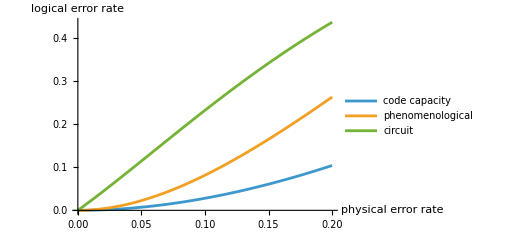

```mathematica
Module[{bf = QECCode["BitFlipCode"], capacity, phenomenological, circuit},
    capacity = QECLogicalErrorRate[bf, QECNoiseModel["BitFlip", p]];
    phenomenological = QECLogicalErrorRate[bf, QECNoiseModel["BitFlip", p, "MeasurementError" -> p], "Rounds" -> 1];
    circuit = QECLogicalErrorRate[bf, QECNoiseModel["Circuit", p], "Rounds" -> 1];
    Plot[
        Evaluate[{capacity, phenomenological, circuit}], {p, 0, 1/5},
        PlotLegends -> {"code capacity", "phenomenological", "circuit"},
        AxesLabel -> {"physical error rate", "logical error rate"},
        ImageSize -> 380
    ]
]
```

Code capacity and the phenomenological level are both quadratic in p and differ by a constant factor — 3 p^2 against 10 p^2. The circuit-level curve is a different shape entirely, and the next section is about why.

One caveat on that figure, and it is the book's: "A threshold in a phenomenological model should not be confused with the threshold derived from a full circuit model; they are not at all comparable" (§10.4). The three curves share an axis but not a quantity — the phenomenological p is a rate per qubit per round, the circuit-level p a rate per location, and the phenomenological model ignores how many gates a syndrome bit costs. Read the picture as one code losing ground as assumptions are dropped, not as three thresholds being compared.

## What circuit-level noise actually costs

Two facts fall out of these polynomials that are hard to state without them. Both are about the extraction circuit rather than the code, and both are exact.

Duality is a property of the codes, not of the circuits that measure them. The bit-flip and phase-flip codes are the same code with X and Z exchanged; both are [[3,1,1]], and under depolarizing noise at code capacity their rates are identical. At circuit level they are not:

```mathematica
Module[{lead = Normal[Series[#, {p, 0, 1}]] &},
    {lead @ QECLogicalErrorRate[QECCode["BitFlipCode"], QECNoiseModel["Circuit", p], "Rounds" -> 1],
     lead @ QECLogicalErrorRate[QECCode["PhaseFlipCode"], QECNoiseModel["Circuit", p], "Rounds" -> 1]}
]
```

{(32 p)/15,(112 p)/15}

The asymmetry is entirely the rotations. The phase-flip code's generators are X-type, so its extraction needs eight H gates that the bit-flip code's does not, and each is a fresh depolarizing location sitting on a data qubit. Switch the one-qubit-gate noise off and the two codes agree again, to the coefficient:

```mathematica
Module[{noise = QECNoiseModel["Circuit", <|"TwoQubit" -> p, "Measurement" -> p, "Reset" -> p|>],
        lead = Normal[Series[#, {p, 0, 1}]] &},
    {lead @ QECLogicalErrorRate[QECCode["BitFlipCode"], noise, "Rounds" -> 1],
     lead @ QECLogicalErrorRate[QECCode["PhaseFlipCode"], noise, "Rounds" -> 1]}
]
```

{(32 p)/15,(32 p)/15}

This extraction circuit stops a distance-three code correcting single faults. The five-qubit code has distance 3, so at code capacity and at the phenomenological level its logical error rate starts at p^2: any one error is corrected. With this circuit it starts at p:

```mathematica
Normal @ Series[
    QECLogicalErrorRate[QECCode["5QubitCode"], QECNoiseModel["Circuit", p], "Rounds" -> 1],
    {p, 0, 1}
]
```

(29 p)/5

Note the phrasing: this is a defect of the gadget, not a property of circuit-level noise. Gottesman's §10.2 exists precisely so that circuit noise need not cost the exponent — a gadget satisfying its propagation properties keeps a distance-three code at p^2 under circuit noise. Order p is the signature of a construction that does not satisfy them.

The mechanism is the hook error, and it is worth being exact about, because the direction of the CNOTs here is the mirror of figure 12.1b's and the obvious transcription is wrong. With the ancilla as target, an X on the ancilla reaches no data qubit at all — CNOT carries X only from control to target, so it sits there and flips one readout. The fault that spreads is a Z (hence also a Y): CNOT carries Z from target back to control, the ancilla keeps its Z, and it lands on every data qubit the ladder has still to touch. After the un-rotation the residual is exactly the un-extracted tail of the generator — a mid-ladder Z on the five-qubit code's XZZXI leaves IZZXI, IIZXI or IIIXI — and, being a sub-product of the generator, it does not fire that generator's own check in the round it happened. A Z before the first CNOT leaves the whole generator, which is a stabilizer and harmless; after the last, nothing. Only mid-ladder hurts.

Count what that does to the decoder's job. At the phenomenological level every single fault has its own detector signature, so no single fault is ever ambiguous. With this circuit the signatures collide, and some of the colliding faults do different things to the logical qubit — at which point no decoder reading detectors alone can tell them apart.

```mathematica
Module[{ambiguity},
    ambiguity[code_, noise_] := Module[{dem, d, o, grouped},
        dem = QECDetectorModel[code, noise, 1];
        d = dem["DetectorMatrix"]; o = dem["ObservableMatrix"];
        grouped = GroupBy[Range[Length[d]], d[[#]] &, DeleteDuplicates[o[[#]] & /@ #] &];
        <|"faults" -> Length[d], "distinct signatures" -> Length[grouped],
          "ambiguous signatures" -> Count[grouped, alternatives_ /; Length[alternatives] > 1]|>
    ];
    Dataset @ <|
        "phenomenological" -> ambiguity[QECCode["5QubitCode"], QECNoiseModel["Depolarizing", 1/1000, "MeasurementError" -> 1/1000]],
        "circuit" -> ambiguity[QECCode["5QubitCode"], QECNoiseModel["Circuit", 1/1000]]
    |>
]
```

Nineteen faults, nineteen distinct signatures, none ambiguous — against 288 faults collapsing onto 71 signatures of which 29 carry conflicting logical effects. The code did not get worse; the circuit measuring it is not fault tolerant.

This is the gap that verified ancillas exist to close, and the book spends a chapter on it: cat states (§12.1.2–12.1.3) feeding Shor error correction (§12.2), Steane error correction (§12.3), Knill error correction (§12.4), with §12.5 comparing their costs.

Three of those are now built, and they close the gap in the direction the number above measures. QECCatState prepares and verifies the cat, with the set of checks derived rather than assumed. QECPauliMeasurement spends it on a transversal controlled-P and repeats with a majority vote (§12.1.4, Theorem 12.1); measuring the same generator the same circuit-level way, one fault now leaves at most one data error where the bare ancilla leaves four. QECErrorCorrection is Steane EC, and it fills the slot between repetitions that Theorem 12.1 needs, chosen for the reason §12.3.3 gives: its ancilla and measurement errors enter additively, so it needs no repeated syndrome measurement at all.

Two things are still missing, and both are named rather than implied. Shor and Knill EC are not built. And the encoded |0⟩ and |+⟩ that Steane EC consumes are prepared here by the code's own non-fault-tolerant encoder, so the gadget is fault tolerant given a clean ancilla — which is precisely the part §12.3.1 calls "the complicated part of Steane EC" and defers to chapter 13. That cost is measured rather than waved at: a fault in the interaction leaves one data error, a fault in the preparation leaves up to four.

The next three sections are those gadgets from the outside.

## Verified cat states

A cat state |0…0⟩+|1…1⟩ is the ancilla that makes the controlled-P transversal: one ancilla qubit per letter of P, each touching one data qubit, so a single fault cannot reach several of them. QECCatState[m] gives the preparation circuit together with the parity checks that verify it.

```mathematica
QECCatState[4]["Instructions"]
```

{{R,1},{R,2},{R,3},{R,4},{H,1},{CNOT,1,2},{CNOT,2,3},{CNOT,3,4},{R,5},{CNOT,2,5},{CNOT,3,5},{MH,5}}

Which pairs to check is the interesting question, and the book leaves the set open — "if we do this on enough pairs of qubits, any single fault in the circuit originally constructing the cat state will be picked up by the checks". Here it is derived instead, by propagating every single fault of the preparation and keeping the X patterns that matter. Two reductions make the set small: X^(⊗m) stabilises the cat, so a pattern and its complement are one error, and a canonical weight of one is a single data error, which the code corrects.

```mathematica
QECCatState[4]["DangerousPatterns"]
```

{{0,0,1,1}}

That single pattern is the book's own figure 12.3b, recovered rather than transcribed.

"ChecksCoverQ" is the proof obligation rather than a remark: a False says the chosen pairs miss a dangerous pattern, which means the gadget is not fault tolerant. The count follows a rule the book does not state — m-3 checks suffice, and m==2 and m==3 need none at all:

```mathematica
Dataset @ Association @ Table[
    m -> With[{cat = QECCatState[m]},
        <|"checks" -> Length[cat["Pairs"]], "dangerous" -> Length[cat["DangerousPatterns"]],
          "covered" -> cat["ChecksCoverQ"]|>],
    {m, 2, 7}]
```

The check outcomes are heralds, not syndrome bits — a nonzero one means discard the attempt — which is why the logical error rate carries an acceptance alongside it when a gadget post-selects.

## Fault-tolerant measurement of a Pauli

QECPauliMeasurement[code, P] spends the cat. One attempt applies the transversal controlled-P and reads the eigenvalue out with a Hadamard transform, so the parity of the weight of the measured string is the answer; the whole gadget repeats that 2t+1 times with a fresh cat each time and takes the majority (Theorem 12.1).

```mathematica
Module[{m = QECPauliMeasurement[QECCode["5QubitCode"], "ZZZZZ"]},
    AssociationMap[m, {"Weight", "Repetitions", "CatQubits", "Qubits", "Measurements", "Heralds"}]]
```

<|Weight→5,Repetitions→3,CatQubits→{6,7,8,9,10},Qubits→11,Measurements→15,Heralds→6|>

The number the construction exists for, against the bare-ancilla circuit measuring the same operator. "DataWeights" is the residual weight on the data over every single fault the gadget admits, and it is a conditional statement in two ways that the property handles rather than hides: only runs the cat checks accept are counted, and the residual is read modulo P, because X^(⊗m) stabilises the cat and so a pattern and its complement leave the same physical state.

```mathematica
Module[{m = QECPauliMeasurement[QECCode["5QubitCode"], "XZZXI", 1]},
    {m["TransversalQ"], m["DataWeights"]}]
```

{True,{0,1}}

One fault, one data error — where the same generator measured with one shared bare ancilla leaves four. That is the hook error gone, in the units the section above priced it in.

What repetition does not fix is the honest boundary, and the gadget says so. If the codeword already carries an error E with EP==-PE, every repetition reads the flipped eigenvalue alike and the majority is confidently wrong — "no matter how many times we repeat it" (§12.1.4). So "MeasurementCorrectQ" is False until an error-correction sub-gadget is spliced between repetitions, and "OpenAssumptions" names what is still assumed:

```mathematica
Module[{m = QECPauliMeasurement[QECCode["SteaneCode"], "IZIZIZI"]},
    {m["MeasurementCorrectQ"], m["ErrorCorrection"], m["OpenAssumptions"]}]
```

{False,None,{No error correction is spliced between repetitions, so a data error anticommuting with the measured Pauli defeats every repetition alike (Got26 sec. 12.1.4). The gadget handles ancilla faults only.}}

## Steane error correction

QECErrorCorrection[code] is the gadget that fills that slot. It is CSS-only, and for a reason rather than by restriction: the construction runs on transversal CNOT being the logical CNOT.

Two halves. The bit-flip half puts an ancilla block in encoded |+⟩ and runs transversal CNOT from data to ancilla — on the encoded states CNOT|ψ⟩|+⟩==|ψ⟩|+⟩, so nothing happens logically, but the gate still copies bit flips into the ancilla where measuring them is harmless. The phase half uses encoded |0⟩, the CNOT the other way, and a transversal Hadamard so the same Z-basis readout sees phase errors.

```mathematica
Module[{ec = QECErrorCorrection[QECCode["SteaneCode"]]},
    AssociationMap[ec, {"DataQubits", "AncillaQubits", "Qubits", "Measurements", "TransversalQ"}]]
```

<|DataQubits→7,AncillaQubits→{8,9,10,11,12,13,14},Qubits→14,Measurements→14,TransversalQ→True|>

Why this gadget and not Shor EC: §12.3.3 asks whether Steane EC needs repeating and answers no, because the errors are additive. The measured classical error is e+f+g — the true data error, the ancilla's, and the measurement's — so correcting by it leaves f+g, and "a single-qubit error in the ancilla can only produce a single-qubit error in the final state. This is in contrast to Shor EC, where a single ancilla error changing one bit of the error syndrome could totally change the error we deduce."

That is a claim to check rather than quote, and the gadget reports both halves of the answer:

```mathematica
Module[{ec = QECErrorCorrection[QECCode["SteaneCode"]]},
    AssociationMap[ec, {"RepetitionsNeeded", "DataWeights", "PreparationDataWeights"}]]
```

<|RepetitionsNeeded→1,DataWeights→{0,1},PreparationDataWeights→{0,1,2,3,4}|>

One fault in the interaction leaves one data error. One fault in the ancilla preparation leaves up to four, because that preparation is still the code's non-fault-tolerant encoder. The split is the open assumption made quantitative, and "OpenAssumptions" states it in words.

Splicing it in completes the structure Theorem 12.1 asks for. The composed gadget still leaves one data error per fault, and inherits the sub-gadget's open assumption rather than hiding it behind that True:

```mathematica
Module[{p = First[QECCode["SteaneCode"]["LogicalZ"]]},
    {QECPauliMeasurement[QECCode["SteaneCode"], p]["MeasurementCorrectQ"],
     QECPauliMeasurement[QECCode["SteaneCode"], p, "ErrorCorrection" -> "Steane"]["MeasurementCorrectQ"],
     QECPauliMeasurement[QECCode["SteaneCode"], p, "ErrorCorrection" -> "Steane"]["DataWeights"]}]
```

{False,True,{0,1}}

And the CSS restriction is enforced rather than documented. The five-qubit code can have a cat measurement, since that works for any code, but not Steane error correction:

```mathematica
QECErrorCorrection[QECCode["5QubitCode"]]
```

QECErrorCorrection::css: Steane error correction needs a CSS code; this one is not CSS. Its generators must each be purely X-type or purely Z-type.

$Failed

## Handing the rate machinery a different extraction

Everything above measures the bare-ancilla circuit, because that is the circuit QECDetectorModel and QECLogicalErrorRate route through. "Extraction" is the option that changes it, and it is on both:

```mathematica
QECDetectorModel[QECCode["5QubitCode"], QECNoiseModel["Circuit", 1/1000], 1,
    "Extraction" -> "Transversal"]["Faults"]
```

624

Only half the fault-tolerant construction can cross over, and the reason is worth stating because it is a property of the formalism rather than of the implementation. A detector error model is a matrix: the effect of a set of faults is the XOR of their rows, and the exact fold, the decoder table and the Stim export all rest on that. Theorem 12.1's gadget takes a majority over 2t+1 repetitions, and majority is not linear, so it cannot sit inside a detector model at all.

What can is transversality — which is the half that fixes the hook error anyway, repetition never having been what cured it. A cat readout's syndrome bit is the parity of its m bits (eqs. 12.1–12.3), and parity is linear. Repetition then stays where it already was, across rounds, handled by the detectors. So "Transversal" is not a weaker "FaultTolerant"; it is the composition the detector formalism admits, and therefore the one whose rate can be computed.

What that buys, counted the same way the section above counted it. With the bare ancilla, 288 faults collapse onto 71 detector signatures of which 29 carry conflicting logical effects. With a transversal extraction — more than twice as many fault locations — 624 faults collapse onto 72 signatures of which only 4 do:

```mathematica
Module[{ambiguity},
    ambiguity[dem_] := Module[{d = dem["DetectorMatrix"], o = dem["ObservableMatrix"], grouped},
        grouped = GroupBy[Range[Length[d]], d[[#]] &, DeleteDuplicates[o[[#]] & /@ #] &];
        <|"faults" -> Length[d], "signatures" -> Length[grouped],
          "ambiguous" -> Count[grouped, alt_ /; Length[alt] > 1]|>];
    Dataset @ <|
        "bare ancilla" -> ambiguity[QECDetectorModel[QECCode["5QubitCode"], QECNoiseModel["Circuit", 1/1000], 1]],
        "transversal" -> ambiguity[QECDetectorModel[QECCode["5QubitCode"], QECNoiseModel["Circuit", 1/1000], 1,
            "Extraction" -> "Transversal"]]|>]
```

And the four that survive are all shots the experiment throws away. Every one is a fault in the cat's own preparation that leaves a weight-two X pattern — exactly what the verification check is there to catch. Condition on the checks accepting, which is the only case that is kept, and no single fault is ambiguous at all:

```mathematica
Module[{dem, d, o, h, keep, grouped},
    dem = QECDetectorModel[QECCode["5QubitCode"], QECNoiseModel["Circuit", 1/1000], 1,
        "Extraction" -> "Transversal"];
    d = dem["DetectorMatrix"]; o = dem["ObservableMatrix"]; h = dem["HeraldMatrix"];
    keep = Select[Range[Length[d]], Total[h[[#]]] === 0 &];
    grouped = GroupBy[keep, d[[#]] &, DeleteDuplicates[o[[#]] & /@ #] &];
    <|"accepted faults" -> Length[keep], "signatures" -> Length[grouped],
      "ambiguous" -> Count[grouped, alt_ /; Length[alt] > 1]|>]
```

<|accepted faults→484,signatures→67,ambiguous→0|>

That zero is the fault-tolerance property, and getting it to show up in the rate took fixing the decoder to match. The decoder only ever runs on an accepted shot, so a fault that trips a verification check cannot have happened; leaving it in the hypothesis space let the lightest-set rule claim a detector pattern on behalf of a fault the experiment had already discarded, and that claim displaced the real explanation. The table is now built from the accepted rows. It is the decoder-side twin of the filter the measurement gadget applies to its residual weight — both statements are conditional on acceptance, and both are wrong if the condition is dropped on one side only.

So, the number this layer was built to produce. The five-qubit code has distance three, so at code capacity its rate starts at p^2: any one error is corrected. With the bare-ancilla extraction it starts at p. With a transversal one the exponent comes back — measured, by evaluating the rate at two physical rates a factor of two apart and reading the slope off:

```mathematica
Module[{exponent, five = QECCode["5QubitCode"]},
    exponent[opts___] := N @ Log[
        QECLogicalErrorRate[five, QECNoiseModel["Circuit", 1/1000], "Rounds" -> 1, opts] /
        QECLogicalErrorRate[five, QECNoiseModel["Circuit", 1/2000], "Rounds" -> 1, opts]
    ] / Log[2];
    Dataset @ <|"bare ancilla" -> exponent[],
                "transversal" -> exponent["Extraction" -> "Transversal"]|>]
```

One and two. That is the hook error shown to be a defect of the gadget rather than a property of circuit-level noise — which is what §10.2 exists to make possible, and what the 29p/5 two sections above was the price of not having.

Two things that number is not. It is a post-selected rate, and the acceptance travels with it — about 0.98 at p==10^-3, and the layer reports it rather than quietly dividing it out:

```mathematica
N @ QECLogicalErrorRate[QECCode["5QubitCode"], QECNoiseModel["Circuit", 1/1000], All,
    "Rounds" -> 1, "Extraction" -> "Transversal"]
```

<|Rate→0.00205313,Acceptance→0.979712,Failure→0.00201147|>

The rate is the failure divided by the acceptance. And it still rests on the ancilla preparation being clean, since the cat is built by a non-fault-tolerant chain and only its dangerous patterns are checked; that is the same chapter-13 assumption Steane EC names, and it is why the four ambiguous signatures existed to be conditioned away in the first place.

## Several blocks, and the gate between them

Everything so far lives on one block. A QECCode is n physical qubits carrying k logical ones, and a circuit numbers its qubits 1…n with ancillas after — which is enough for a memory experiment, and is why the p^2 above could be measured without any of this. It is not enough for anything that computes.

A logical qubit is a block. So a logical two-qubit gate is a gate between two blocks, and Theorem 13.2 needs 2m blocks for a gate touching m of them. QECRegister is where blocks become addressable. Block b owns qubits (b-1)n+1…bn, stated once so that nothing has to guess it:

```mathematica
Module[{reg = QECRegister[QECCode["SteaneCode"], 2]},
    AssociationMap[reg, {"Blocks", "BlockQubits", "Qubits", "StabilizerCount", "LogicalQubits"}]]
```

<|Blocks→2,BlockQubits→7,Qubits→14,StabilizerCount→12,LogicalQubits→2|>

A single-block circuit moves into a block with "Lift", which touches the qubit slots and nothing else:

```mathematica
QECRegister[QECCode["SteaneCode"], 2]["Lift", {{"R", 1}, {"H", 2}, {"CNOT", 1, 2}}, 2]
```

{{R,8},{H,9},{CNOT,8,9}}

A register of one block is the identity on all of it — same label matrix, same generators, same circuits — which is what keeps the rest of the layer unaffected by this existing.

The one gate between blocks is the transversal CNOT: a CNOT applied qubit by qubit, so each qubit of one block touches exactly the corresponding qubit of the other and nothing else. That is the property that stops a single fault from spreading inside either block, and it is the one Steane error correction already rested on two sections ago.

It was cited there. Here it is checked, by conjugating the logical operators through the gate and reading the images off:

```mathematica
QECRegister[QECCode["SteaneCode"], 2]["LogicalAction", 1, 2]
```

<|{X,1,1}→IIXIXXIIIXIXXI,{X,2,1}→IIIIIIIIIXIXXI,{Z,1,1}→IZIZIZIIIIIIII,{Z,2,1}→IZIZIZIIZIZIZI|>

(X̄)_1→(X̄)_1(X̄)_2, (X̄)_2→(X̄)_2, (Z̄)_1→(Z̄)_1, (Z̄)_2→(Z̄)_1(Z̄)_2 — which is the action of a CNOT on the logical pair.

Acting correctly on the logical operators is only half of it. The gate also has to map the stabilizer group to itself, or it takes the state out of the code space and its logical action is beside the point. For the Steane code none of the twelve register generators leaves the group; for the five-qubit code, which is not CSS, all eight of them do:

```mathematica
Module[{images},
    images[r_] := Module[{instr = r["TransversalCNOT", 1, 2], nq = r["Qubits"], group},
        group = QECCode[r["Generators"]];
        Count[
            QECPauli[Wolfram`QuantumFramework`QEC`PackageScope`registerConjugate[instr, nq, QECPauli[#]["Vector"]]]["String"] & /@ r["Generators"],
            g_ /; ! group["StabilizerMemberQ", g]]];
    Dataset @ <|
        "Steane (CSS)" -> images[QECRegister[QECCode["SteaneCode"], 2]],
        "five-qubit (not CSS)" -> images[QECRegister[QECCode["5QubitCode"], 2]]|>]
```

That is the restriction QECErrorCorrection enforces, seen at its source rather than at the gadget that inherits it.

One detail worth keeping, because it is what makes the group test the one that decides. On the five-qubit code the Z half of the action still comes out right — (Z̄)_2 does map to (Z̄)_1(Z̄)_2, exactly as a CNOT would. Only the X half breaks:

```mathematica
Module[{reg5 = QECRegister[QECCode["5QubitCode"], 2], act, x, z, prod},
    act = reg5["LogicalAction", 1, 2];
    x = (QECPauli[#]["String"] &) /@ reg5["LogicalVectors"]["X"];
    z = (QECPauli[#]["String"] &) /@ reg5["LogicalVectors"]["Z"];
    prod[s1_, s2_] := (QECPauli[s1] ** QECPauli[s2])["String"];
    <|"Z half behaves" -> (act[{"Z", 2, 1}] === prod[z[[1]], z[[2]]]),
      "X half behaves" -> (act[{"X", 1, 1}] === prod[x[[1]], x[[2]]])|>]
```

<|Z half behaves→True,X half behaves→False|>

Checking the logical action alone would have passed half the time and been wrong.

## The gates a code gives you for free

A code that can only remember is half a code. Chapter 11 asks the other half: which gates can act on the encoded qubit without letting one fault spread inside a block? For a stabilizer code the question turns out to be one about symmetry. Apply the same one-qubit gate U to every qubit of the block, separately. If that map sends the stabilizer group to itself, the gate is a valid gadget — and whatever it then does to X̄ and Z̄ is the logical gate you have performed.

QECTransversalGate asks both halves and answers with the second. The Hadamard on the seven-qubit code:

```mathematica
QECTransversalGate[QECCode["SteaneCode"], "H"]["LogicalAction"]
```

<|{X,1}→Z,{Z,1}→X|>

X̄→Z̄ and Z̄→X̄: the transversal Hadamard is the logical Hadamard (eq. 11.18–11.19).

Now ask the same of S, and the answer is not the one the name suggests:

```mathematica
Module[{s = QECTransversalGate[QECCode["SteaneCode"], "S"]},
    <|"logical action" -> s["LogicalAction"], "logical gate" -> s["LogicalGate"]|>]
```

<|logical action→<|{X,1}→-Y,{Z,1}→Z|>,logical gate→Sdg|>

One minus sign, and it is a different gate. X̄→-Ȳ with Z̄ fixed is the action of S^†, not of S. The transversal S performs the inverse of the gate it is built from — so if you want the logical S on this code, you apply the transversal S^†.

The sign is one line of Pauli algebra, and it is worth seeing on its own:

```mathematica
(QECPauli["XXXXXXX"] ** QECPauli["ZZZZZZZ"])["String"]
```

iYYYYYYY

X̄ Z̄==i Y^(⊗7), and Ȳ==i X̄ Z̄, so Y^(⊗7)==-Ȳ (eq. 11.22). Seven copies of Y==iXZ do not give the logical Y; they give minus it.

This is the one place in the layer where a sign carries the answer. Everywhere else — the Pauli frame, the detector model, the whole memory experiment — conjugation modulo sign was enough, and the frame propagator drops phases for good reasons. Here a sign-blind conjugation reports "S" and is wrong, so this file carries the Z_4 phase through every step and asks membership of a routine that knows a generator's true phase.

The S^† is not an accident of S. The transversal U performs the logical U^*, the complex conjugate, which is visible across the whole one-qubit gate set at once:

```mathematica
Dataset @ AssociationMap[
    QECTransversalGate[QECCode["SteaneCode"], #]["LogicalGate"] &,
    {"H", "S", "Sdg", "V", "Vdg", "X", "Y", "Z"}]
```

Real matrices come back unchanged; the ones with an i in them come back inverted.

How many gates does that leave? On the seven-qubit code, all of them — every one of the twenty-four one-qubit Cliffords is a valid gadget, which is what the chapter singles this code out for. On the five-qubit code, exactly half:

```mathematica
Dataset @ <|
    "Steane" -> Length[QECTransversalGate[QECCode["SteaneCode"], All]],
    "five-qubit" -> Length[QECTransversalGate[QECCode["5QubitCode"], All]]|>
```

And half is not none. The five-qubit code has no transversal H and no transversal S, but it does have the cyclic Clifford X→Y→Z→X, which is S followed by H:

```mathematica
Module[{five = QECCode["5QubitCode"], g},
    g = QECTransversalGate[five, {"S", "H"}];
    <|"H alone" -> QECTransversalGate[five, "H"]["TransversalQ"],
      "S then H" -> g["TransversalQ"],
      "its logical action" -> g["LogicalAction"]|>]
```

<|H alone→False,S then H→True,its logical action→<|{X,1}→-Y,{Z,1}→-X|>|>

Which is the useful form of a statement people usually shorten to "the five-qubit code has no transversal gates". It has a different set of them, and asking is one call.

Between two blocks the question has the CNOT as its answer. The previous section checked that modulo sign; here the phases are carried, and two more gates come free with the same symmetry:

```mathematica
Dataset @ AssociationMap[
    QECTransversalGate[QECCode["SteaneCode"], #]["LogicalGate"] &, {"CNOT", "CZ", "SWAP"}]
```

On the five-qubit code the same gate is not a gadget at all, and section 11.4 says why in one direction: demanding that transversal CNOT preserve the stabilizer forces the generators to be X-only or Z-only, which is the definition of a CSS code.

H, S and CNOT generate the Clifford group, so the seven-qubit code performs the whole logical Clifford group transversally — with the caveat above, that each gate arrives conjugated. What is missing is everything outside that group: no transversal T, on this or any code of this kind, and that is chapter 13's problem rather than a gap in this one.

## Putting the gadgets together: FT(C)

Every gadget so far has been built and checked on its own. Definition 10.6 is the instruction for spending them all at once. Take an ideal circuit C, replace each of its qubits with a block of the code, replace each of its locations with the corresponding gadget, and after every preparation, gate and storage gadget put an error correction gadget on each block involved — never after a measurement gadget, because its output is classical and classical circuits are assumed not to fail.

QECFaultTolerantCircuit is that substitution. Here is a four-location circuit — prepare two logical qubits, Hadamard one, CNOT them, measure both — made fault tolerant on the seven-qubit code:

```mathematica
QECFaultTolerantCircuit[
    {{"R", 1}, {"R", 2}, {"H", 1}, {"CNOT", 1, 2}, {"M", 1}, {"M", 2}},
    QECCode["SteaneCode"]]["Gadgets"]
```

Two of those rows are worth pointing at. The storage gadget is block 2 waiting while block 1 gets its Hadamard: a wait is a location, the book's storage gadget is "just putting a wait location for all physical qubits in the code", and it earns an error correction gadget like any other. It emits no instructions and it costs — which is the difference between an honest overhead and a count of typed-out gates. And there are six corrections, not four: one per live block per layer, stopping when the block is measured.

Definition 10.6 also defines what that costs, in three ratios, so they are properties rather than something you assemble yourself:

```mathematica
QECFaultTolerantCircuit[
    {{"R", 1}, {"R", 2}, {"H", 1}, {"CNOT", 1, 2}, {"M", 1}, {"M", 2}},
    QECCode["SteaneCode"]]["Overheads"]
```

<|Size→263,Qubits→14,Depth→77/4|>

Seven locations become 1841. Fourteen physical qubits per logical one — seven for the block and seven for its own error-correction workspace, one workspace per block so that the corrections of a layer run in parallel rather than queueing. And nineteen and a quarter times the depth. Those are the numbers a fault-tolerance threshold has to beat, and they are why the threshold is a statement about rates rather than about counts.

Now the detail that makes this more than bookkeeping. The gadget for a logical S is not the transversal S:

```mathematica
Union @ Map[First,
    QECFaultTolerantCircuit[{{"R", 1}, {"S", 1}}, QECCode["SteaneCode"]]["GadgetInstructions", "Gate"]]
```

{Sdg}

Asked for a logical S, the assembler emitted a transversal S^† — because that is the word whose logical action is S, as the previous section measured. It never emits "the transversal version of the gate it was asked for"; it asks which word performs the requested logical gate. A protocol assembled by name would compute the complex conjugate of the intended circuit and look perfectly healthy doing it, and on the engine the difference is visible: assembled properly the encoded qubit ends in the +1 eigenstate of Ȳ, and assembled by name in the -1 eigenstate.

The classical side is tracked too. The logical bit of a measurement gadget is the parity of a few of its outcomes, and those outcomes sit in a record otherwise full of error-correction syndromes, so a decoder has to be told where:

```mathematica
Module[{ft = QECFaultTolerantCircuit[
        {{"R", 1}, {"R", 2}, {"H", 1}, {"CNOT", 1, 2}, {"M", 1}, {"M", 2}},
        QECCode["SteaneCode"]]},
    <|"measurements in the whole circuit" -> ft["Measurements"],
      "the ones that make logical qubit 1" -> ft["Readouts"][1]|>]
```

<|measurements in the whole circuit→98,the ones that make logical qubit 1→{86,88,90}|>

Three outcomes out of ninety-eight, being the support of Z̄==IZIZIZI inside the seventh-last block of measurements.

What this protocol is not, stated rather than hidden — ft["OpenAssumptions"] says all three. The preparation gadget is the code's own encoder, which is not fault tolerant, and so are the ancillas of every correction: that is chapter 13's work and the same debt the error correction gadget already reported. The gate gadgets are transversal, so the gate set is Clifford — Definition 10.5 asks for a universal set, and a circuit with a T in it is refused rather than approximated. And corrections stay in the Pauli frame, so nothing in the emitted circuit is classically conditioned.

## Handing it to Stim

Stim (arXiv:2103.02202) is the community's reference stabilizer simulator, and the source of the detector error model as an explicit object. The point of connecting to it rather than competing with it is that the two are good at different things: it samples fast and large, this layer derives exactly and symbolically. Writing the memory experiment out in its syntax buys an independent check on all of the above, and a path to the decoders built on top of it.

The emitted circuit encodes first — Stim starts in |0…0⟩, which is not a codeword for a general code, and a memory experiment that does not start inside the code space has a meaningless first round of detectors — then runs the noisy rounds, then a noiseless one:

```mathematica
Column @ Take[
    StringSplit[QECStim[QECCode["BitFlipCode"], QECNoiseModel["Circuit", 1/200], 2], "
"],
    14
]
```

# 3 data qubits, 2 check ancillas, 2 noisy rounds, Z-basis memory
# emitted by QECStim
# --- encode ---
H 1
H 0
CZ 1 2
H 1
CZ 0 1
H 0
# --- round 1 ---
R 3
X_ERROR(0.005) 3
CX 0 3
DEPOLARIZE2(0.005) 0 3

The structure scales as it should: one detector per check per round, plus the final noiseless round, and a single logical observable. Three noisy rounds of the Steane code's six checks give four layers of six:

```mathematica
Module[{source = QECStim[QECCode["SteaneCode"], QECNoiseModel["Circuit", 1/500], 3]},
    {StringCount[source, "DETECTOR"], StringCount[source, "OBSERVABLE_INCLUDE"]}
]
```

{24,1}

One asymmetry is deliberate. QECLogicalErrorRate asks whether the decoder got the residual error's whole class right, covering logical X and logical Z damage at once, because that is the right question for an unknown logical state. A Stim memory experiment is single-basis by construction — prepare (|0)_L⟩, keep it, measure Z̄ — so the emitted circuit declares one observable and "Observable" chooses which. The detector part is basis-independent, and that is where the two models are compared.

That comparison has been run. Five cases — three at circuit level, two at phenomenological, including the non-CSS five-qubit code whose Y generators are the only thing exercising the square-root-of-X rotation — with 58 detector firing rates and 5 observable flip rates computed exactly here and sampled over two million shots there. Everything agrees within 2.7 standard errors, and PyMatching decodes every exported circuit unchanged, which is a second and structural check: a malformed circuit does not produce a detector error model that decomposes into a matching graph.

## Where this comes from

Every claim above is either computed by the package and checked against an independent oracle, or taken from one of these. Section numbers are Gottesman's 2026 Stabilizer Codes and Quantum Error Correction unless the thesis is named.

| Topic | Source
       | Stabilizer formalism, standard form, logical operators, distance | Thesis §3.2, §4.1
       | Concatenation, qubit removal, pasting | Thesis §3.5
       | The [[n,n-2,2]] family, the quantum Singleton bound | Thesis §8.1
       | Repetition codes as neighbouring-pair checks | Thesis §2.2
       | The encoder | Book §6.4.1, Procedure 6.6 with Table 6.1
       | Circuit-level noise: locations, faults, one rate per location type | Book §10.1.1, Definitions 10.1–10.3
       | What fault tolerance formally requires | Book §10.2
       | The phenomenological model, and thresholds not being comparable across levels | Book §10.4
       | The extraction circuit, and its non-fault-tolerance | Book §12.1.1, figures 12.1a and 12.1b
       | Measuring the whole syndrome and then repeating | Book §12.2.2, figures 12.6 and 12.7
       | How many repetitions a fault-tolerance guarantee needs | Book §12.2.2
       | Verified ancillas: cat states, Shor, Steane, Knill | Book §12.1.2–12.1.3, §12.2, §12.3, §12.4, §12.5
       | Why surface-code practice uses the non-fault-tolerant circuit anyway | Book §12.5.1
       | Reusing ancillas across rounds | Book §15.4, §15.4.3
       | Serial extraction, waiting, and why idle noise matters more not less | Book §15.5.1, §15.5.2
       | Detectors as differences of repeated noisy syndromes | Dennis, Kitaev, Landahl, Preskill, arXiv:quant-ph/0110143
       | The detector error model as an object, and the Stim syntax | Gidney, arXiv:2103.02202
       | Minimum-weight matching on a detector model | Higgott and Gidney, PyMatching

Two places where this note is deliberately outside the sources, and says so rather than implying cover it does not have. The exact circuit-level rate is a closed-form polynomial obtained by folding fault locations into a distribution over effects; §10.4 lists rigorous proof, simulation, analytical estimate and hybrid methods for getting at a threshold, and this is none of them. And the decoder optimises over the whole spacetime fault history, which is the strategy §12.2.2 raises and then sets aside as hard to analyse in general — so the numbers here are exact error rates for a stated protocol, not fault-tolerance proofs.

## What is exact, and what is not

Five limits are worth stating plainly, because a result that looks exact and is not is worse than an estimate.

Enumeration is capped. The code-capacity route walks all 4^n errors, so it is bounded by $QECExactEnumerationLimit, which is 4^10 by default. The nine-qubit Shor code takes about a second; past ten qubits, pass a sample count instead and get an estimate with error bars you control.

The exact circuit-level route is capped by its state space, not its fault count. Folding locations into a distribution over effects costs 2^((r+1)m+2k) per step, bounded by $QECExactDetectorLimit. That grows in the rounds, so the Steane code is exact at one round and must be sampled at three. Sampling draws the true channels, not the independent-mechanism approximation attached to the detector model's rows, so the sampled number is not the weaker answer — only the slower-converging one.

The decoder is chosen at a probe rate. Maximum likelihood needs to compare probabilities, and with a symbolic rate there is nothing to compare. The argmax is therefore resolved at a small fixed rate, $QECDecoderProbeRate. Once chosen the decoder is a fixed function, and the polynomial reported for it is exact at every p — but it is the polynomial for that decoder, not for a decoder retuned at each p.

The circuit-level decoder is minimum weight over fault subsets, up to a reach. It is exact at low weight and explodes combinatorially past it, so it stops and says so at $QECDecoderSubsetLimit. A matching decoder plugs in at the detector model and returns the same kind of answer; that is roadmap work, not a gap in the model.

The default extraction circuit is not fault tolerant, and is not claimed to be. Its ancillas are bare rather than verified, which is what produces the hook errors measured above. That is an honest property of the circuit rather than an approximation: the rate reported is the true rate for this circuit, and §12.1.1 is where to read what it costs. "Extraction" -> "Transversal" replaces it with one that is — conditionally: the rate it returns is post-selected on the cat checks accepting, and carries its acceptance, and the cat preparation itself is still the non-fault-tolerant chain of §12.1.3 rather than a chapter-13 gadget.

Zero idle noise is the default, and it is the one optimistic assumption left. Idling is now modelled rather than missing: the schedule is recovered from the instruction list by ASAP list scheduling, a qubit no instruction of a time step touches is waiting, and each such slot carries its three Paulis. But "Idle" still defaults to zero, and every circuit-level number in this note is computed at that default. Generators are extracted sequentially, so the circuit waits more than a parallel one would, not less; §15.5.1 quantifies the storage rate that serialisation multiplies, and §15.5.2 says an ill-defined time step is to be defined and its padding charged, never dropped. Set "Idle" and the numbers get worse, in the direction this circuit is already weakest.

## How this is checked

Nothing above is trusted because the package computed it. Every fast routine is cross-checked against a slow, obvious one, and the checks run as a suite of 685 tests.

| What | Checked against
       | Pauli algebra, products and phases | Dense 2^n×2^n matrices built from scratch
       | Row layout | The engine's own tableau, row for row
       | Syndromes | Expectation values measured on an actual stabilizer state
       | Encoding circuits | The state they prepare, checked check by check
       | Structural results | Gottesman's published values — X̄==ZIIZX, the [[4,2,2]] generators
       | CSS and concatenation | The textbook codes they must reproduce, as groups and with signs
       | Noise probabilities | The mixture the engine's channels actually return
       | Logical error rate | A closed-form binomial tail, and an independent sampled route
       | The extraction circuit | code["Syndrome", …], and the circuit run as a state on the engine
       | Detectors and faults | Stim's own sampler, detector by detector, over two million shots
       | Circuit-level rate | The code-capacity polynomial it must reduce to, and a sampled route
       | Idle noise and the schedule | The Stim export, DEPOLARIZE1 line for line against the model's slots
       | Cat states | Every single fault propagated through the preparation, against the check set
       | The encoded ancillas | The engine: $
       | Fault tolerance of the gadgets | The residual data weight over every single fault, against the bare-ancilla circuit measuring the same operator
       | That a transversal extraction can go in a detector model at all | Its effect on 200 random fault pairs, against the XOR of their rows
       | That it restores the exponent | The rate at two physical rates a factor of two apart, slope read off
       | That a transversal CNOT is the logical CNOT | Conjugating the logical operators through it, and the stabilizer group mapping to itself
       | That a transversal gate is the gate you think it is | The gate's own matrix, conjugated with the Z_4 phase carried; the logical gate against the complex conjugate of the physical one
       | That the assembled FT(C) computes C | The engine: the gate gadgets alone, run with no faults, must leave the blocks in the state the ideal circuit would
       | The exported circuit | PyMatching, which decodes it unchanged
       | The encoder and codewords | V^†V==1, V V^† against ∏(1+g)/2, and V^†P̄ V==P for the code's own logical operators
       | The logical channel | The exact logical error rate, identically, and its action on a state against its own weights
       | Knill–Laflamme, symplectically | Its dense definition over the codewords
       | Noise read from a channel | The channel's superoperator, and the named channels' known weights
       | A decoder object | The engine's own decoding table, entry for entry, herald filter included
       | The retired names | The value each returned before, and one warning per session

The habit is worth keeping when extending the layer: a result checked only against the code that produced it is not checked.

Related Guides

WolframQuantumComputationFrameworkpaclet:Wolfram/QuantumFramework/guide/WolframQuantumComputationFramework

Related Tech Notes

## Metadata

### Categorization

Tutorial

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/StabilizerCodes

### Keywords

quantum error correction

stabilizer code

syndrome

decoder

logical operator

code distance

encoding circuit

CSS code

concatenation

noise model

logical error rate

syndrome extraction

detector error model

circuit-level noise

memory experiment

Stim